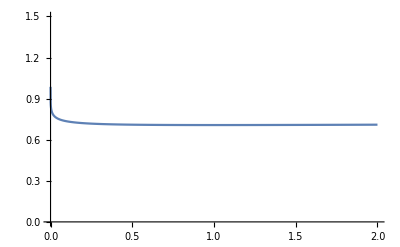

```mathematica
Plot[{(√(x+√x))/(√(√x)+√x)},{x,0,2},PlotLegends->"Expressions",PlotRange->{0,1.5}]
```

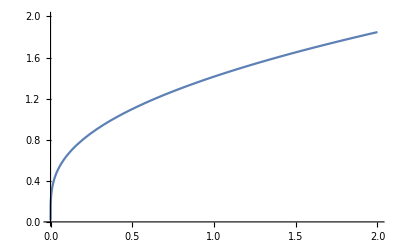

```mathematica
Plot[{√(x+√x)},{x,0,2},PlotLegends->"Expressions",PlotRange->{0,2}]
```

```mathematica
N[ Integrate[√(√x)+√x,{x,0,2}],15]
```

3.78834946716848

```mathematica
N[ Integrate[√(x+√x),{x,0,2}],10]
```

2.689521305

```mathematica
Integrate[6-x^2-y^2-z^2-u^2-v^2,{x,0,0.9},{y,0,0.8},{z,0,0.9},{u,0,2},{v,0,1.3}]
```

5.64408

```mathematica
0.9*0.8*0.9*2*1.3
```

1.6848

```mathematica
Limit[D[(√(x+√x))/(√(√x)+√x),x],x->0]
```

Indeterminate

```mathematica
D[(√(x+√x))/(√(√x)+√x),x]
```

(1+1/(2 √x))/(2 (x^(1/4)+√x) √(√x+x))-((1/(4 x^(3/4))+1/(2 √x)) √(√x+x))/((x^(1/4)+√x)^2)